```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsOld=ReadList[FileNameJoin[{Directory[],"files/PureIntegralBasis1-151.txt"}]];
PureIntegralsNew=PureIntegralsOld;
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
$P=2^31-1;
CayleyEntry[i_,j_]:=Module[{mat},
If[i==0 && j==0 ,
Return[0];
];
If[i==0 || j==0 ,
Return[1];
];

If[i==j,
mat=2msq[i]/.intMasses;
Return[mat];
];
If[i<j,
mat=((msq[i]/.intMasses)+(msq[j]/.intMasses)-Expand[(Sum[q[n],{n,i,j-1}])^2])/.mandelstamScalarProducts/.kinematics;
Return[mat];
];
If[i>j,
mat=CayleyEntry[j,i];
Return[mat];
];
]
cutCayley[mat_,l_]:=Module[{res},
res=mat;
res=Delete[res,l];
res=Transpose[Delete[Transpose[res],l]];
res
]
```

# Gram Change

```mathematica
CanonicalGramVec={p[1],p[2],p[3],p[4]};
Ganonical5ptGram=16Det[Expand[Table[CanonicalGramVec[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]]/.kinematics/.mandelstamScalarProducts]//Factor
vectors={p[3],p[4],p[5],p[6]};
Gram1=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange1=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[4],p[5],p[6],p[1]};
Gram2=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange2=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[5],p[6],p[1],p[2]};
Gram3=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange3=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[3],p[2],p[1],p[6]};
Gram4=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange4=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[2],p[3],p[4],p[5]};
Gram5=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange5=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;

vectors={p[3],p[4],p[5],p[6]};
Gram6=16Det[Expand[Table[vectors[[i]]vectors[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;
GramChange6=16Det[Expand[Table[vectors[[i]]CanonicalGramVec[[j]],{i,1,4},{j,1,4}]/.p4cons]/.kinematics/.mandelstamScalarProducts]//Factor;


Gram5Repl={root[Gram1]->GramChange1/root[Ganonical5ptGram],root[Gram2]->GramChange2/root[Ganonical5ptGram],root[Gram3]->GramChange3/root[Ganonical5ptGram],root[Gram4]->GramChange4/root[Ganonical5ptGram],root[Gram5]->GramChange5/root[Ganonical5ptGram],root[Gram6]->GramChange6/root[Ganonical5ptGram]};
```

s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2

# Diagram 152/158 (Basis1 - 151)

hxb[-1,1,1,1,0,0,1,1,0,0,0,0,0]

hxb[0,1,1,1,0,0,1,1,0,0,0,0,0]

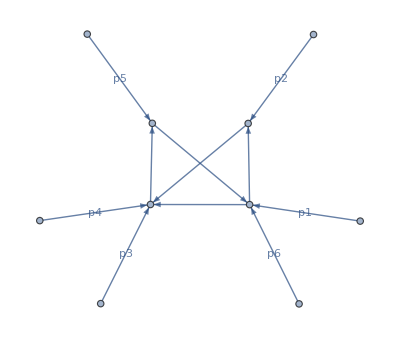

```mathematica
PureIntegralsOld[[152]]
PureIntegralsOld[[158]]
plotDiagram[PureIntegralsOld[[158]]]
```

```mathematica
v45=Expand[Expand[2(p[1]+p[6])*p[2]/.p4cons]/.kinematics/.mandelstamScalarProducts]
v15=Expand[Expand[2(p[3]+p[4])*p[2]/.p4cons]/.kinematics/.mandelstamScalarProducts]
 BasisChange[1]=ep^4(-s16+s345+s234-s34)
 BasisChange[2]=ep^3/PR[4](s234-s34)(-s16+s345)
```

-s16+s345

s234-s34

ep^4 (-s16+s234-s34+s345)

(ep^3 (s234-s34) (-s16+s345))/PR[4]

# Diagram 154/160 (Basis1 - 151)

hxb[-1,1,1,1,0,1,0,1,0,0,0,0,0]

hxb[0,1,1,1,0,1,0,1,0,0,0,0,0]

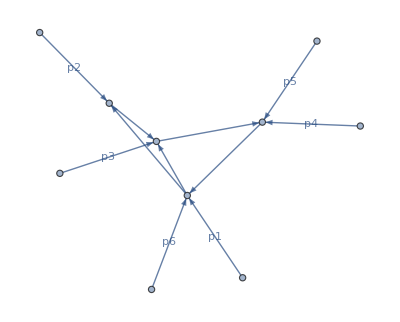

```mathematica
PureIntegralsOld[[154]]
PureIntegralsOld[[160]]
plotDiagram[PureIntegralsOld[[154]]]
```

```mathematica
v45=Expand[Expand[2(p[2])*p[3]/.p4cons]/.kinematics/.mandelstamScalarProducts]
v15=Expand[Expand[2(p[2])*(p[1]+p[6])/.p4cons]/.kinematics/.mandelstamScalarProducts]
 BasisChange[3]=ep^4(s23-s16+s345)
 BasisChange[4]=ep^3/PR[4](s23)(-s16+s345)
```

s23

-s16+s345

ep^4 (-s16+s23+s345)

(ep^3 s23 (-s16+s345))/PR[4]

# Diagram 187, 188 (Basis1 - 151)

hxb[1,1,0,1,0,1,0,1,-1,0,0,0,0]

hxb[1,1,0,1,0,1,0,1,0,0,0,0,0]

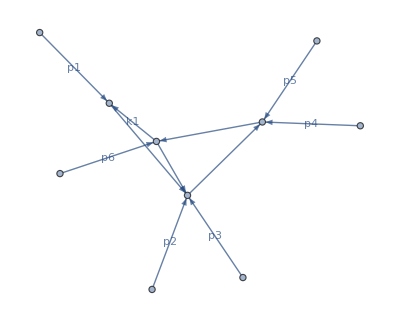

```mathematica
PureIntegralsOld[[187]]
PureIntegralsOld[[188]]
plotDiagram[PureIntegralsOld[[188]]]
```

```mathematica
v45=Expand[Expand[2(p[1])*p[6]/.p4cons]/.kinematics/.mandelstamScalarProducts]
v15=Expand[Expand[2(p[1])*(p[2]+p[3])/.p4cons]/.kinematics/.mandelstamScalarProducts]
 BasisChange[5]=ep^4(-mt2+s16+s123-s23)
 BasisChange[6]=ep^3/PR[4](-mt2+s16)(s123-s23)
```

-mt2+s16

s123-s23

ep^4 (-mt2+s123+s16-s23)

(ep^3 (-mt2+s16) (s123-s23))/PR[4]

# Diagram 163, 166, 169, 170, 171, 172 (Basis1 - 151)

hxb[1,-1,1,1,0,0,1,1,0,0,0,0,0]

hxb[1,0,1,1,-1,0,1,1,0,0,0,0,0]

hxb[1,0,1,1,0,0,1,1,-2,0,0,0,0]

hxb[1,0,1,1,0,0,1,1,-1,0,0,0,0]

hxb[1,0,1,1,0,0,1,1,0,-1,0,0,0]

hxb[1,0,1,1,0,0,1,1,0,0,0,0,0]

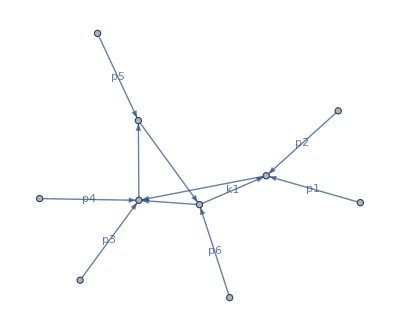

```mathematica
PureIntegralsOld[[163]]
PureIntegralsOld[[166]]
PureIntegralsOld[[169]]
PureIntegralsOld[[170]]
PureIntegralsOld[[171]]
PureIntegralsOld[[172]]
plotDiagram[PureIntegralsOld[[172]]]
```

```mathematica
BasisChange[7]=ep^4
BasisChange[8]=ep^3/PR[1]
BasisChange[9]=ep^3/PR[3]
BasisChange[10]=ep^3/PR[4]
BasisChange[11]=ep^3/PR[7]
BasisChange[12]=ep^3/PR[8]
```

ep^4

ep^3/PR[1]

ep^3/PR[3]

ep^3/PR[4]

ep^3/PR[7]

ep^3/PR[8]

# Diagram 164, 167, 174, 175, 176, 177 (Basis1 - 151)

hxb[1,-1,1,1,0,1,0,1,0,0,0,0,0]

hxb[1,0,1,1,-1,1,0,1,0,0,0,0,0]

hxb[1,0,1,1,0,1,0,1,-2,0,0,0,0]

hxb[1,0,1,1,0,1,0,1,-1,0,0,0,0]

hxb[1,0,1,1,0,1,0,1,0,-1,0,0,0]

hxb[1,0,1,1,0,1,0,1,0,0,0,0,0]

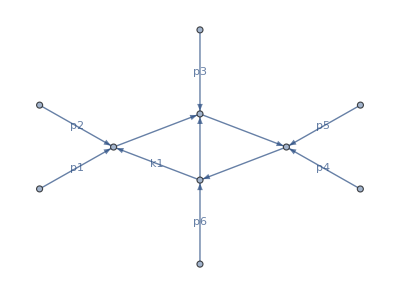

```mathematica
PureIntegralsOld[[164]]
PureIntegralsOld[[167]]
PureIntegralsOld[[174]]
PureIntegralsOld[[175]]
PureIntegralsOld[[176]]
PureIntegralsOld[[177]]
plotDiagram[PureIntegralsOld[[177]]]
```

```mathematica
BasisChange[13]=ep^4
BasisChange[14]=ep^3/PR[1]
BasisChange[15]=ep^3/PR[3]
BasisChange[16]=ep^3/PR[4]
BasisChange[17]=ep^3/(PR[6])
BasisChange[18]=ep^3/PR[8]
```

ep^4

ep^3/PR[1]

ep^3/PR[3]

ep^3/PR[4]

ep^3/PR[6]

ep^3/PR[8]

# Assemble basis

```mathematica
(*SelectInts={8,9,10,11,75,76,77,78,79,112,113,114,122,127,131,132,152,158,154,160,187,188};*)
(*SelectInts={7,8,9,10,11,18,19,22,75,76,77,78,79,80,86,87,88,104,112,113,114,115,122,127,131,132,152,158,154,160,187,188,163,166,169,170,171,172,152,154,158,160,163,164,166,167,169,170,171,172,174,175,176,177,187,188};*)
SelectInts=
{7,8,9,10,11,18,19,22,75,76,77,78,79,80,86,87,88,104,112,113,114,115,122,127,131,132,152,158,154,160,187,188,163,166,169,170,171,172,164,167,174,175,176,177}
SelectIntsNotPure=Pick[SelectInts,Thread[SelectInts>151]]
SelectIntsPure=Pick[SelectInts,Thread[SelectInts<=151]]

PureIntegralsNew[[152]]=Collect[PureIntegralsOld[[158]]*BasisChange[1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[158]]=Collect[PureIntegralsOld[[158]]*BasisChange[2]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[154]]=Collect[PureIntegralsOld[[160]]*BasisChange[3]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[160]]=Collect[PureIntegralsOld[[160]]*BasisChange[4]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[187]]=Collect[PureIntegralsOld[[188]]*BasisChange[5]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[188]]=Collect[PureIntegralsOld[[188]]*BasisChange[6]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[163]]=Collect[PureIntegralsOld[[172]]*BasisChange[7]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[166]]=Collect[PureIntegralsOld[[172]]*BasisChange[8]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[169]]=Collect[PureIntegralsOld[[172]]*BasisChange[9]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[170]]=Collect[PureIntegralsOld[[172]]*BasisChange[10]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[171]]=Collect[PureIntegralsOld[[172]]*BasisChange[11]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[172]]=Collect[PureIntegralsOld[[172]]*BasisChange[12]//Expand,{_hxb,root[___]},Together];

PureIntegralsNew[[164]]=Collect[PureIntegralsOld[[177]]*BasisChange[13]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[167]]=Collect[PureIntegralsOld[[177]]*BasisChange[14]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[174]]=Collect[PureIntegralsOld[[177]]*BasisChange[15]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[175]]=Collect[PureIntegralsOld[[177]]*BasisChange[16]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[176]]=Collect[PureIntegralsOld[[177]]*BasisChange[17]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[177]]=Collect[PureIntegralsOld[[177]]*BasisChange[18]//Expand,{_hxb,root[___]},Together];


SubPureInts=PureIntegralsNew[[SelectInts]](*/.Gram5Repl*);
Newsqrts=(Cases[SubPureInts,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Oldsqrts=(Cases[PureIntegralsOld/.Gram5Repl,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
sqrtSetNew=Join[Oldsqrts,Newsqrts]//DeleteDuplicates;
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],sqrtSetNew];
Export[FileNameJoin[{NotebookDirectory[],"TrianglePureInts.txt"}],SubPureInts];
```

{7,8,9,10,11,18,19,22,75,76,77,78,79,80,86,87,88,104,112,113,114,115,122,127,131,132,152,158,154,160,187,188,163,166,169,170,171,172,164,167,174,175,176,177}

{152,158,154,160,187,188,163,166,169,170,171,172,164,167,174,175,176,177}

{7,8,9,10,11,18,19,22,75,76,77,78,79,80,86,87,88,104,112,113,114,115,122,127,131,132}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 mt2 s12+(-mt2-s12+s345)^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,-4 mt2 s56+s56^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),(mt2 s12-mt2 s123+s123 s345-s12 s45)^2}

# Export New Basis

```mathematica
StillNonPureInts=DeleteElements[PureIntegralsOld[[152;;]],PureIntegralsOld[[SelectIntsNotPure]]];
NewPureInts=PureIntegralsNew[[SelectIntsNotPure]];
NewBasis=Join[PureIntegralsNew[[;;151]],NewPureInts,StillNonPureInts]//EchoFunction[Length];
NewBasis=NewBasis/.Gram5Repl;
Newsqrts=(Cases[NewBasis,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],Newsqrts];

Export[FileNameJoin[{Directory[],"files/LinearBasis-169.txt"}],NewBasis];
```

241

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,s12^2 s23^2-2 s12^2 s23 s234+2 s12 s123 s23 s234+s12^2 s234^2-2 s12 s123 s234^2+s123^2 s234^2+2 s12 s123 s23 s34-2 s12 s23^2 s34+2 s12 s123 s234 s34-2 s123^2 s234 s34+2 s12 s23 s234 s34+2 s123 s23 s234 s34+s123^2 s34^2-2 s123 s23 s34^2+s23^2 s34^2-2 s12 s23^2 s56+2 s12 s23 s234 s56-2 s123 s23 s234 s56-4 s12 s23 s34 s56+2 s123 s23 s34 s56-2 s23^2 s34 s56+s23^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56),(mt2 s12-mt2 s123+s123 s345-s12 s45)^2}